```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="/home/huangys/mount/DATA/Documents/2-d-data";}];
```

```mathematica
Kernel1[ϕn_][x_?NumberQ]:=NIntegrate[ϕn[p]/(p-x)^2,{p,0,1}];
Kernel2[ϕn_,ϕm_][x_?NumberQ,z_?NumberQ,ω_?NumberQ]:=NIntegrate[(ϕn[y]ϕm[z/ω y])/(y-x)^2,{y,0,1}];
```

```mathematica
Kernel2PV[ϕn_,ϕm_][x_?NumberQ,z_?NumberQ,ω_?NumberQ]:=NIntegrate[(ϕn[y]ϕm[ω/z y])/(y-x)^2,{y,0,x-λ}]+NIntegrate[(ϕn[y]ϕm[ω/z y])/(y-x)^2,{y,x+λ,1}]-2(ϕn[x]ϕm[ω/z x])/λ ;
```

```mathematica
A[ω_][ϕ1_,ϕ2_,ϕ3_]:=1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"](*r1=1*)
```

```mathematica
FBBplusDD[z_,ω_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=(1+ℂ)(-HeavisideTheta[ω-z](1-ω)/z NIntegrate[ϕ2[(1-ω)/(1-z)x]ϕ4[x](ϕ1[y]ϕ3[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,0,1}]+HeavisideTheta[z-ω](1-z)/ω NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}])
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=(*-*)(√((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2))/(2 M1^2)+M2^2/(2 M1^2)-M3^2/(2 M1^2)+1/2
```

```mathematica
zfp[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2-√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2));
```

```mathematica
zfn[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2+√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2))
```

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=1/(2 (-M1^2+M1^2 z-M2^2 z))(-M1^2+M1^2 z-M2^2 z-M3^2 z+M4^2 z+M3^2 z^2-M4^2 z^2-√(-4 (-M1^2+M1^2 z-M2^2 z) (-M3^2 z+M3^2 z^2)+(M1^2-M1^2 z+M2^2 z+M3^2 z-M4^2 z-M3^2 z^2+M4^2 z^2)^2))
```

```mathematica
ωfn[z_][M1_,M2_,M3_,M4_]:=1/(2 (-M1^2+M1^2 z-M2^2 z))(-M1^2+M1^2 z-M2^2 z-M3^2 z+M4^2 z+M3^2 z^2-M4^2 z^2+√(-4 (-M1^2+M1^2 z-M2^2 z) (-M3^2 z+M3^2 z^2)+(M1^2-M1^2 z+M2^2 z+M3^2 z-M4^2 z-M3^2 z^2+M4^2 z^2)^2))
```

```mathematica
ASin[n_][m1_]:=
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
]
```

```mathematica
At[n_][ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
],{m1,ma,mb,δm}]
```

```mathematica
B2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.1,0.5,0.1}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.6,0.8,0.02}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.8,0.9,0.01}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.9,0.99,0.005}]
]
```

```mathematica
B2π2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[z=zfp[ω][M1,M2,M3,M4];If[z∈Reals,Print["z=",z,"    ω=",ω];{ω,FBBplusDD[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},],{ω,0.1,0.9,0.01}](*~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.6,0.8,0.02}]~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.8,0.9,0.01}]~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.9,0.99,0.005}]*)
]
```

#### Debug

```mathematica
Block[{mQ=√2000,mq=1},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Φπ[x_]=ϕxπ;
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Φπ[x_]=ϕxπ;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];]
```

Wavefunction build complete.

```mathematica
Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-6},Print[ω];Print[(1-z)/(1-ω)];NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1-(1-x)(1-z)/ω-λ}]+NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1}]-NIntegrate[2ϕ4[(1-z)/(1-ω)x]ϕ2[x]ϕ3[1-(1-x)(1-z)/ω] ϕ1[ω/z(1-(1-x)(1-z)/ω)]/λ,{x,0,1}]]//AbsoluteTiming
```

0.426125

0.0174254

{249.276,-0.001878-9.56303×10^-7 ⅈ}

```mathematica
Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-6},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1-(1-x)(1-z)/ω-λ}]]//AbsoluteTiming
```

{197.481,8.61397}

#### Do this integration and check the imaginary part:

```mathematica
Table[Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-n},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1}]],{n,1,10}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{299.438,{0.+1.25487×10^121 ⅈ,0.000790897+1.36209×10^30 ⅈ,-0.00445847+34.0405 ⅈ,0.0571155-0.000104621 ⅈ,0.812728-0.0000104019 ⅈ,8.50068-9.56303×10^-7 ⅈ,85.5106,855.74,8558.16,85582.5}}

```mathematica
Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-6},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1},Method->"LocalAdaptive"]]//AbsoluteTiming
```

{262.15,8.50069}

```mathematica
Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-6},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1},Method->"AdaptiveMonteCarlo"]]//AbsoluteTiming
```

{40.6154,9.82805}

```mathematica
Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-6},Plot3D[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1}]]
```

$Aborted

```mathematica
Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-6,x=0.5,y=0.5},ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2]
```

-5.21792×10^-8

```mathematica
Block[{z=0.99,ω=ωfn[0.99][M1,M2,M3,M4],λ=10^-6},NIntegrate[2ϕ4[(1-z)/(1-ω)x]ϕ2[x]ϕ3[1-(1-x)(1-z)/ω] ϕ1[ω/z(1-(1-x)(1-z)/ω)]/λ,{x,0,1}]]//AbsoluteTiming
```

{6.26253,17.1165}

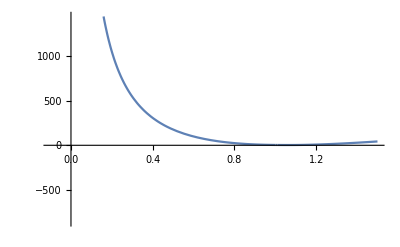

```mathematica
Plot[(1-z)/(1-1/(2 (-M1^2+M1^2 z-M2^2 z))(-M1^2+M1^2 z-M2^2 z-M3^2 z+M4^2 z+M3^2 z^2-M4^2 z^2-√(-4 (-M1^2+M1^2 z-M2^2 z) (-M3^2 z+M3^2 z^2)+(M1^2-M1^2 z+M2^2 z+M3^2 z-M4^2 z-M3^2 z^2+M4^2 z^2)^2))),{z,-0.1,1.5}]
```

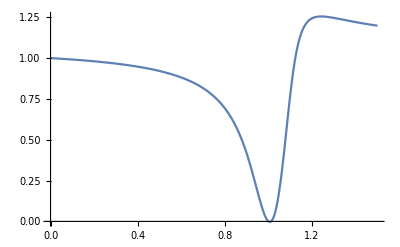

```mathematica
Plot[(1-z)/(1-1/(2 (-M1^2+M1^2 z-M2^2 z))(-M1^2+M1^2 z-M2^2 z-M3^2 z+M4^2 z+M3^2 z^2-M4^2 z^2+√(-4 (-M1^2+M1^2 z-M2^2 z) (-M3^2 z+M3^2 z^2)+(M1^2-M1^2 z+M2^2 z+M3^2 z-M4^2 z-M3^2 z^2+M4^2 z^2)^2))),{z,0,1.5}]
```

```mathematica
(M1^2-M3^2)/(M1^2-M2^2-M3^2+M4^2)
```

1.12295

```mathematica
M1^2/(M1^2-M2^2)
```

1.01174